# Form Factors

## Init

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/luchinsky/Dropbox/DskD/Work/bc/bc_chi_npi/Math

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
Clear[extractFF];
extractFF::usage="extractFF[json, num]";
extractFF[json_, n_, fact_:1]:=Module[{name, data},
name = json⟦3,2,n,1,2⟧;
data = json⟦3,2,n,5,2,All,3,2⟧;
data⟦All,2⟧=fact*data⟦All,2⟧;
Return[<|"name"->name,"data"->data|>]
]
```

```mathematica
Clear[extractNames];
extractNames[json_]:=Module[{names = json⟦3,2,All,1,2⟧}, Table[{i,names⟦i⟧},{i,Length[names]}]];
```

## Ebert

### χ_c(1P)

```mathematica
tab$fPlus = Import["../literatute/Ebert_FFs/chi0_fPlus.csv"];
tab$fMinus = Import["../literatute/Ebert_FFs/chi0_minusFminus.csv"];
tab$fMinus⟦All,2⟧=-tab$fMinus⟦All,2⟧;
```

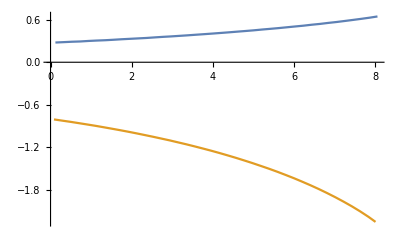

```mathematica
ListPlot[{tab$fPlus, tab$fMinus}, Joined->True]
```

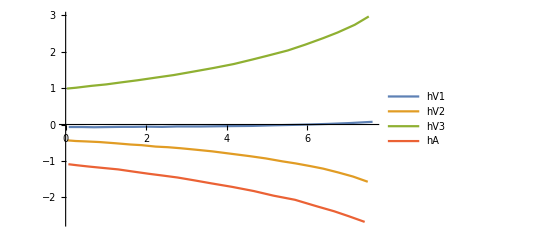

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_1P.json"];
tab$hV1 = extractFF[chic1,1]["data"];
tab$hV2 = extractFF[chic1,2, -1]["data"];
tab$hV3 = extractFF[chic1,3]["data"];
tab$hA = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

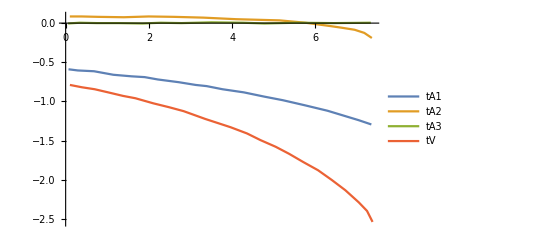

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_1P.json"];
tab$tA3 = extractFF[chic2, 1]["data"];
tab$tA2 = extractFF[chic2, 2]["data"];
tab$tA1 = extractFF[chic2, 3, -1]["data"];
tab$tV = extractFF[chic2, 4,-1]["data"];
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

### χ_c(2P)

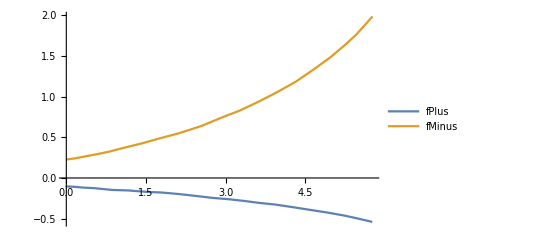

```mathematica
chic0 = Import["../literatute/Ebert_FFs/fig3_chic0_2P.json"];
tab$fPlus$2P = extractFF[chic0,1,-1]["data"];
tab$fMinus$2P = extractFF[chic0,2]["data"];
ListPlot[{tab$fPlus$2P, tab$fMinus$2P}, Joined->True, PlotLegends->{"fPlus", "fMinus"}]
```

{hV1,hV2,hA,-hV3}

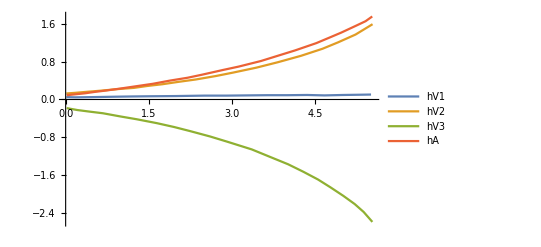

```mathematica
chic1 = Import["../literatute/Ebert_FFs/fig3_chic1_2P.json"];
chic1⟦3,2,All,1,2⟧
tab$hV1$2P = extractFF[chic1,1]["data"];
tab$hV2$2P = extractFF[chic1,2]["data"];
tab$hA$2P = extractFF[chic1,3]["data"];
tab$hV3$2P = extractFF[chic1,4,-1]["data"];
ListPlot[{tab$hV1$2P,tab$hV2$2P,tab$hV3$2P, tab$hA$2P}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

{tA3,tA2,tA1,tV}

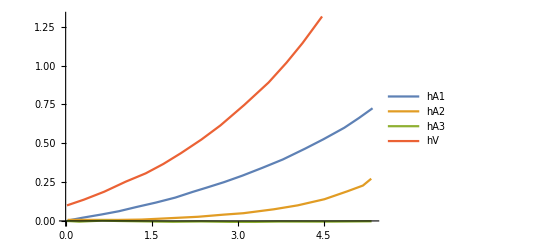

```mathematica
chic2 = Import["../literatute/Ebert_FFs/fig3_chic2_2P.json"];
Print[chic2⟦3,2,All,1,2⟧];
tab$tA3$2P = extractFF[chic2,1]["data"];
tab$tA2$2P = extractFF[chic2,2]["data"];
tab$tA1$2P = extractFF[chic2,3]["data"];
tab$tV$2P = extractFF[chic2,4]["data"];
ListPlot[{tab$tA1$2P,tab$tA2$2P,tab$tA3$2P, tab$tV$2P}, Joined->True, PlotLegends->{"hA1", "hA2", "hA3", "hV"}]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=0.2735114574549966 + 0.02698177783795792*q2 + 0.0004438591230092838*pow(q2,2) + 0.00023394089715202517*pow(q2,3);
*fMinus=-0.7888608969785541 - 0.10052789894587946*q2 + 0.0028122053015600472*pow(q2,2) - 0.0015941397716725178*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=-0.07249517884406438 + 0.006386114470446252*q2 - 0.0016598461472340164*pow(q2,2) + 0.00043125401922510393*pow(q2,3);
*hV2=-0.42708574288736423 - 0.08150607461417403*q2 + 0.00655250512925111*pow(q2,2) - 0.002089171872485879*pow(q2,3);
*hV3=0.9721190093276546 + 0.14785518940757297*q2 - 0.010128808927653912*pow(q2,2) + 0.0033475878397617523*pow(q2,3);
*hA=-1.0807476041824315 - 0.1250995787006434*q2 + 0.00032468802756664515*pow(q2,2) - 0.0016479191668232192*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=-0.7593279619789294 - 0.14373638874539618*q2 + 0.015428531108854306*pow(q2,2) - 0.0037404399820982963*pow(q2,3);
*tA1=-0.5845892322932432 - 0.05829150603138564*q2 + 0.0003828588805250468*pow(q2,2) - 0.0007578111067025861*pow(q2,3);
*tA2=0.0939174867271461 - 0.029819354099933058*q2 + 0.01373975840177015*pow(q2,2) - 0.0019524446633583286*pow(q2,3);
*tA3=-0.0020369655557486233 + 0.0033852618872049524*q2 - 0.0008299552762151167*pow(q2,2) + 0.00006460810519319177*pow(q2,3);

```mathematica
ffFitRule$2P = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]<>"$2P"], fitFunc,fitParams,q2]]
,{ff, ffList}];
```

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,1,2}];
str
```

*fPlus=-0.1036523606752476 - 0.04296031595098163*q2 + 0.0006186521497841605*pow(q2,2) - 0.0010752967931538292*pow(q2,3);
*fMinus=0.2146487305494538 + 0.15242330361247391*q2 - 0.010551275203077543*pow(q2,2) + 0.006370594008633078*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,3,6}];
str
```

*hV1=0.04439115389660447 + 0.019084131704071243*q2 - 0.002604726424031802*pow(q2,2) + 0.00018149830649920272*pow(q2,3);
*hV2=0.1172598023033568 + 0.12069109270869871*q2 - 0.012606920768015749*pow(q2,2) + 0.006864162691296876*pow(q2,3);
*hV3=-0.16364417143981633 - 0.22885046487359123*q2 + 0.030520612375782352*pow(q2,2) - 0.012027948054465212*pow(q2,3);
*hA=0.07973359107787653 + 0.15842249566142913*q2 - 0.005579327065777525*pow(q2,2) + 0.00560617437583373*pow(q2,3);

```mathematica
str="";
Do[
str=str<>"*"<>ToString[ffFitRule$2P⟦i,1,0⟧]<>"="<>ToString[CForm[ffFitRule$2P[[i,2]]/.Power->pow]]<>";\n"
,{i,7,10}];
str
```

*tV=0.09539971009568 + 0.1323082354062854*q2 + 0.007744430814653726*pow(q2,2) + 0.0052822727875911765*pow(q2,3);
*tA1=-0.0014086383044029733 + 0.06739181582166379*q2 + 0.0036492170862357574*pow(q2,2) + 0.0016746836655900166*pow(q2,3);
*tA2=0.0017971881442419284 + 0.01760619468206874*q2 - 0.010590128853260362*pow(q2,2) + 0.0030609488394743095*pow(q2,3);
*tA3=-0.0008750946774129126 - 0.0005646397692624229*q2 - 0.0007184243134305922*pow(q2,2) + 0.0001459108759474624*pow(q2,3);

### Save

```mathematica
DeleteFile["./mdat/ebert_ff.mdat"];
file = OpenWrite["./mdat/ebert_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule], InputForm]<>"\n"];
WriteString[file, ToString[Definition[ffFitRule$2P], InputForm]<>"\n"];
Close[file];
```

## Wang et al, arXiv:1107:0474 [hep-ph]

```mathematica
json = Import["../literatute/1107.0474/fig3_FF.json"];
```

```mathematica
(* we have distribution over q2max - q2 on the plot! *)
Clear[getMcc];
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
(* 1P masses from PDG *)
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
(* 2P masses are chosen to fit Ebert's distributions *)
getMcc[out_, "2P"]:=Switch[out,"chi_c0", 3862MeV,"chi_c1", 3.9214,"chi_c2",3.967735]
q2Max[out_]:=($MBc-getMcc[out])^2;
```

```mathematica
Clear[reflect];
reflect[tab_,out_]:=Module[{newTab=tab},
newTab⟦All,1⟧=q2Max[out]-newTab⟦All,1⟧;
newTab
];
```

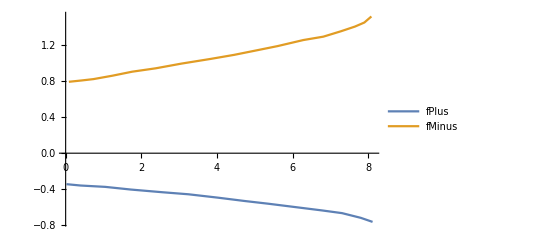

```mathematica
out="chi_c0";
tab$fPlus = extractFF[json, 1, -1]⟦"data"⟧//reflect[#,out]&;
tab$fMinus= extractFF[json, 2]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$fPlus,tab$fMinus}, Joined->True, PlotLegends->{"fPlus","fMinus"}]
```

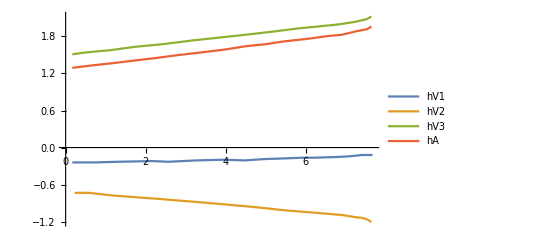

```mathematica
out="chi_c1";
tab$hV1 = extractFF[json, 3, -1]⟦"data"⟧//reflect[#,out]&;
tab$hV2 = extractFF[json, 4, -1]⟦"data"⟧//reflect[#,out]&;
tab$hV3 = extractFF[json, 5 ]⟦"data"⟧//reflect[#,out]&;
tab$hA = extractFF[json, 6 ]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$hV1,tab$hV2,tab$hV3, tab$hA}, Joined->True, PlotLegends->{"hV1", "hV2", "hV3", "hA"}]
```

```mathematica
extractNames[json]
```

(1 | chi0: -sPlus
2 | chi0_sMinus
3 | chi1: -f
4 | chi1: -u1
5 | chi1:u2
6 | chi1:g
7 | chi2:-c1
8 | chi2:-k
9 | chi2:c2
10 | chi2:h)

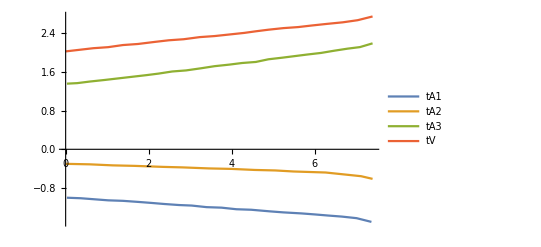

```mathematica
out="chi_c2";
tab$tA2 = extractFF[json, 7, -1]⟦"data"⟧//reflect[#,out]&;
tab$tA1 = extractFF[json, 8, -1]⟦"data"⟧//reflect[#,out]&;
tab$tA3 = extractFF[json, 9]⟦"data"⟧//reflect[#,out]&;
tab$tV = extractFF[json, 10]⟦"data"⟧//reflect[#,out]&;
ListPlot[{tab$tA1, tab$tA2, tab$tA3, tab$tV},Joined->True, PlotLegends->{"tA1", "tA2", "tA3", "tV"}, PlotRange->All]
```

```mathematica
fitFunc=a0+a1 q2 + a2 q2^2+a3 q2^3;
fitParams = DeleteCases[Variables[fitFunc] ,q2]
```

{a0,a1,a2,a3}

```mathematica
ffFitRule$Wang = Table[
ff[q2_]:>Evaluate[ fitFunc/.FindFit[ToExpression["tab$"<>ToString[ff]], fitFunc,fitParams,q2]]
,{ff, ffList}]
```

{fPlus(q2_):>-0.000465616 q2^3+0.002523 q2^2-0.0400244 q2-0.339914,fMinus(q2_):>0.00108867 q2^3-0.00879204 q2^2+0.088168 q2+0.77019,hV1(q2_):>0.000221592 q2^3-0.000913403 q2^2+0.0103316 q2-0.244354,hV2(q2_):>-0.000565963 q2^3+0.00426655 q2^2-0.0602775 q2-0.710388,hV3(q2_):>0.00071155 q2^3-0.00685796 q2^2+0.0899868 q2+1.49342,hA(q2_):>0.000614869 q2^3-0.00513732 q2^2+0.090039 q2+1.27202,tV(q2_):>0.000591919 q2^3-0.00523579 q2^2+0.101539 q2+2.01927,tA1(q2_):>-0.000688005 q2^3+0.00543166 q2^2-0.068395 q2-0.988895,tA2(q2_):>-0.00121872 q2^3+0.00992445 q2^2-0.0475703 q2-0.292165,tA3(q2_):>0.000339803 q2^3-0.00108563 q2^2+0.101109 q2+1.34214}

```mathematica
DeleteFile["./mdat/wang_ff.mdat"];
file = OpenWrite["./mdat/wang_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Wang], InputForm]<>"\n"];
Close[file];
```

```mathematica
str="// Wnang's FF\n\n";
Do[
str=str<>"*"<>ToString[f⟦1,0⟧]<>"="<>ToString[CForm[f⟦2⟧/.Power->pow]]<>";\n"
,{f, ffFitRule$Wang}]
str
```

// Wnang's FF

*fPlus=-0.33991380592027914 - 0.040024442563952885*q2 + 0.0025230010943415723*pow(q2,2) - 0.0004656159966881966*pow(q2,3);
*fMinus=0.7701897692262628 + 0.0881680421897945*q2 - 0.00879204111309994*pow(q2,2) + 0.0010886713551476884*pow(q2,3);
*hV1=-0.24435448046190159 + 0.010331648277938579*q2 - 0.0009134031378323107*pow(q2,2) + 0.00022159216585685204*pow(q2,3);
*hV2=-0.7103876821583478 - 0.0602774820822653*q2 + 0.004266553207625208*pow(q2,2) - 0.000565962924451258*pow(q2,3);
*hV3=1.4934249265375008 + 0.08998682725105182*q2 - 0.006857963573522601*pow(q2,2) + 0.000711550359979238*pow(q2,3);
*hA=1.2720231435712308 + 0.09003897439415781*q2 - 0.005137318246822382*pow(q2,2) + 0.0006148691245052408*pow(q2,3);
*tV=2.0192706161363225 + 0.10153860806900702*q2 - 0.0052357919072080665*pow(q2,2) + 0.0005919186313734745*pow(q2,3);
*tA1=-0.9888948657318037 - 0.0683950179746637*q2 + 0.005431661340191046*pow(q2,2) - 0.0006880049067587609*pow(q2,3);
*tA2=-0.2921648565036161 - 0.04757032020969248*q2 + 0.009924447477444942*pow(q2,2) - 0.0012187229555837636*pow(q2,3);
*tA3=1.3421413598569518 + 0.10110866108376225*q2 - 0.0010856339717409947*pow(q2,2) + 0.0003398028563210277*pow(q2,3);

## Henandez, hep-ph/0607150v3

```mathematica
<<"./mdat/amps.mdat";
```

```mathematica
P = p1+p2; q=p1-p2;
```

```mathematica
ScalarProduct[p2, eps]=0;
```

### chi_c0

```mathematica
out = "chi_c0";
ampH[out]=Calc[FV[P,mu]FPlus + FV[q,mu]Fminus];
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
Solve[#==0&/@(Select[#, FreeQ[#, Pair[__]]&]&/@List@@diff), {fPlus, fMinus}]⟦1⟧
```

{fPlus→FPlus,fMinus→Fminus}

```mathematica
Clear[genFF];
genFF::usage="genFF[out, minF, maxF]";
genFF[out_, minF_, maxF_]:=minF+(maxF-minF)q2/q2Max[out];
```

```mathematica
FPlus = genFF["chi_c0", 0.30, 0.64];
FMinus = genFF["chi_c0", −0.62, −1.35];
```

```mathematica
ffFitRule$Hernandez  = {};
AppendTo[ffFitRule$Hernandez, fPlus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 2]["data"], fitFunc, fitParams,q2]]];
AppendTo[ffFitRule$Hernandez, fMinus[q2_]:>Evaluate[fitFunc/.FindFit[extractFF[json, 1,-1]["data"], fitFunc, fitParams,q2]]];
```

```mathematica
Clear[MBc, Mcc, FPlus, FMinus];
```

### chi_c1

```mathematica
out = "chi_c1";
```

```mathematica
ampH[out]=I(-1/(MBc+Mcc)LeviCivita[mu, a][P,q]V-I((MBc-Mcc)MT[a,mu]A0-FV[P,a]/(MBc+Mcc)(FV[P,mu]Aplus+FV[q,mu]Aminus)));
```

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
```

```mathematica
eqList=#==0&/@(List@@diff);
```

```mathematica
sol=Solve[Flatten[{eqList⟦1;;3⟧, eqList⟦5⟧}],{hA, hV1, hV2, hV3}]
```

{{hA→V,hV1→(A0 MBc-A0 Mcc)/(MBc+Mcc),hV2→-(MBc (Aminus+Aplus))/(MBc+Mcc),hV3→(MBc (Aminus-Aplus))/(MBc+Mcc)}}

```mathematica
GeV=1.; MeV=10^-3 GeV;
$MBc = 6274.47MeV;
getMcc[out_, type_:"1P"]:=Switch[out,"chi_c0", 3414.71MeV,"chi_c1", 3510.67MeV,"chi_c2", 3556.17MeV]
Mcc = getMcc[out];
```

```mathematica
V = genFF[out, 0.92, 1.86];
Aplus=genFF[out, −0.44, −0.78];
Aminus=genFF[out, 0.96, 1.97];
A0=genFF[out, −0.50, −0.32];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
sol
```

{{hA→0.123059 q2+0.92,hV1→0.282449 (0.0235646 q2-0.5),hV2→-0.641224 (0.0877125 q2+0.52),hV3→0.641224 (0.176734 q2+1.4)}}

```mathematica
AppendTo[ffFitRule$Hernandez, hV1[q2_]:>Evaluate[hV1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV2[q2_]:>Evaluate[hV2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hV3[q2_]:>Evaluate[hV3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, hA[q2_]:>Evaluate[hA/.sol⟦1⟧]];
```

```mathematica
Clear[MBc, Mcc, V, Aminus, Aplus, A0];
```

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>-0.00108867 q2^3+0.0179182 q2^2-0.162804 q2+1.4987,fMinus(q2_):>0.000465616 q2^3-0.00890074 q2^2+0.092183 q2-0.753182,hV1(q2_):>0.282449 (0.0235646 q2-0.5),hV2(q2_):>-0.641224 (0.0877125 q2+0.52),hV3(q2_):>0.641224 (0.176734 q2+1.4),hA(q2_):>0.123059 q2+0.92}

### chi_c2

```mathematica
out = "chi_c2";
```

```mathematica
ampH[out]=I(LeviCivita[mu, a][P,q]FV[P,b]T4-I(MT[mu, b]*FV[P,a]T1+FV[P,a]FV[P,b](FV[P,mu]T2+FV[q,mu]T3)))
```

ⅈ (T4 (OverBar[p1]+OverBar[p2])^b (ϵ̄)^(muaOverBar[p1]+OverBar[p2]OverBar[p1]-OverBar[p2])-ⅈ (T1 (OverBar[p1]+OverBar[p2])^a (ḡ)^bmu+(OverBar[p1]+OverBar[p2])^a (OverBar[p1]+OverBar[p2])^b (T2 (OverBar[p1]+OverBar[p2])^mu+T3 (OverBar[p1]-OverBar[p2])^mu)))

```mathematica
diff = (ampH[out]-amplitude[out, "V+A"])//Calc//Collect2[#, Pair[__]]&//ReplaceAll[#, a_[q2]:>a]&;
```

```mathematica
diff
```

(OverBar[p1]^a (ḡ)^bmu (MBc T1-MBc tA1-Mcc tA1))/MBc+T1 OverBar[p2]^a (ḡ)^bmu+(2 ⅈ OverBar[p1]^b (MBc^2 T4+MBc Mcc T4+tV) (ϵ̄)^(amu OverBar[p1]OverBar[p2]))/(MBc (MBc+Mcc))+(OverBar[p1]^a OverBar[p1]^b OverBar[p2]^mu (MBc^2 T2-MBc^2 T3-tA3))/MBc^2+(OverBar[p1]^a OverBar[p1]^b OverBar[p1]^mu (MBc^2 T2+MBc^2 T3-tA2))/MBc^2+(T2+T3) OverBar[p2]^a OverBar[p1]^b OverBar[p1]^mu+(T2+T3) OverBar[p1]^a OverBar[p2]^b OverBar[p1]^mu+(T2+T3) OverBar[p2]^a OverBar[p2]^b OverBar[p1]^mu+(T2-T3) OverBar[p2]^a OverBar[p1]^b OverBar[p2]^mu+(T2-T3) OverBar[p1]^a OverBar[p2]^b OverBar[p2]^mu+2 ⅈ T4 OverBar[p2]^b (ϵ̄)^(amu OverBar[p1]OverBar[p2])+(T2-T3) OverBar[p2]^a OverBar[p2]^b OverBar[p2]^mu

```mathematica
eqList=#==0&/@(List@@diff);
Length[eqList]
```

12

```mathematica
sol=Solve[Flatten[{eqList⟦1⟧,eqList⟦3⟧, eqList⟦5⟧, eqList⟦9⟧}],{tA1, tA2, tA3, tV}]//Simplify
```

{{tA1→(MBc T1)/(MBc+Mcc),tA2→MBc^2 (T2+T3),tA3→MBc^2 (T2-T3),tV→-MBc T4 (MBc+Mcc)}}

```mathematica
T1=genFF[out, 0.97, 1.95];
T2=genFF[out, −0.012, −0.025];
T3=genFF[out, 0.013, 0.030];
T4=genFF[out, 0.013, 0.030];
```

```mathematica
MBc = $MBc; Mcc = getMcc[out];
```

```mathematica
sol
```

{{tA1→0.638257 (0.132627 q2+0.97),tA2→39.369 (0.000541334 q2+0.001),tA3→39.369 (-0.00406 q2-0.025),tV→-61.6821 (0.00230067 q2+0.013)}}

```mathematica
ffFitRule$Hernandez
```

{fPlus(q2_):>-0.00108867 q2^3+0.0179182 q2^2-0.162804 q2+1.4987,fMinus(q2_):>0.000465616 q2^3-0.00890074 q2^2+0.092183 q2-0.753182,hV1(q2_):>0.282449 (0.0235646 q2-0.5),hV2(q2_):>-0.641224 (0.0877125 q2+0.52),hV3(q2_):>0.641224 (0.176734 q2+1.4),hA(q2_):>0.123059 q2+0.92}

```mathematica
AppendTo[ffFitRule$Hernandez,tA1[q2_]:>Evaluate[tA1/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA2[q2_]:>Evaluate[tA2/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tA3[q2_]:>Evaluate[tA3/.sol⟦1⟧]];
AppendTo[ffFitRule$Hernandez, tV[q2_]:>Evaluate[tV/.sol⟦1⟧]];
```

```mathematica
ffFitRule$Hernandez//Length
```

10

```mathematica
DeleteFile["./mdat/hernandez_ff.mdat"];
file = OpenWrite["./mdat/hernandez_ff.mdat"];
WriteString[file, ToString[Definition[ffFitRule$Hernandez], InputForm]<>"\n"];
Close[file];
```